# xCPS: an xAct package for covariant phase space, Noether charges, and entropy

## Companion file for the paper xCPS: an xAct package for covariant phase space, Noether charges, and entropy [arXiv: 2606.05204]

Juan Margalef-Bentabol

juan.margalef@umontreal.ca
Université de Montréal, Canada

## 1. Introduction

```mathematica
<<xAct`xCPS`
$PrePrint=ScreenDollarIndices;
SetOptions[ContractMetric,AllowUpperDerivatives -> True];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCPS` version 1.1.0, {2026,5,23}

CopyRight (C) 2025, Juan Margalef-Bentabol and Laura Sánchez Cotta, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
(* Initial definitions explained later *)
$DefInfoQ=False;
DefConstantSymbol[dimen]
DefManifold[M,dimen,{a,b,c,d,e,f,h,i,j,k,l}]
DefMetric[-1,g[-a,-b],Nabla,{";","∇"}]
PrintAs[RiemannNabla]^="Riem";
PrintAs[RicciNabla]^="Ric";
PrintAs[RicciScalarNabla]^="R";
DefTensor[Phi[],M,PrintAs->"Φ"]
Implode[Nabla[-a][Phi[]]];
Implode[Nabla[-e][RiemannNabla[-a,-b,-c,-d]]];
DefTensor[xi[a],M,PrintAs->"ξ"]
DefScalarFunction[F,{RiemannNabla,NablaRiemannNabla}]
DefScalarFunction[L,{Phi,NablaPhi}]

BianchiRule=MakeRule[{RiemannNabla[a,b,c,d],RiemannNabla[a,c,b,d]-RiemannNabla[a,d,b,c],OrderedQ[{a,b,c,d}]},MetricOn->All];
BianchiContracted1=MakeRule[{Nabla[-e]@RiemannNabla[-a,-c,-d,e],$RicciSign(Nabla[-c]@RicciNabla[-a,-d]-Nabla[-a]@RicciNabla[-c,-d])},MetricOn->All];
BianchiContracted2=MakeRule[{Nabla[-b]@RicciScalarNabla[],2Nabla[-a][RicciNabla[a,-b]]},MetricOn->All];

ApplyBianchi[expr_]:=expr//.BianchiContracted1//.BianchiContracted2//.BianchiRule
```

```mathematica
Lscalar=√(-Detg[])L[Phi,NablaPhi] ;
FirstVariation[Phi][Lscalar]//TotalDerivativeToCovD//Simplification
```

∇_a ((√(-g^OverTilde[~]) (ⅆΦ) ((∂L)/(∂∇Φ)) | a
 ))+√(-g^OverTilde[~]) (ⅆΦ) (((∂L)/(∂Φ))-∇_a ((∂L)/(∂∇Φ)) | a
 )

```mathematica
LGR=√(-Detg[])RicciScalarNabla[];
SymplecticCurrent[][LGR]//ContractMetric//Simplification
EOM[RiemannNabla][LGR]//Simplification
```

1/2 √(-g^OverTilde[~]) (n_∇) | a
  ((ⅆg) |   | b
a |  ⩕∇_b (ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕∇_a (ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕∇_c (ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕∇_a (ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕∇_c (ⅆg) |   |  
a | b))

1/2 √(-g^OverTilde[~]) (-g | a | d
  |   g | b | c
  |  +g | a | c
  |   g | b | d
  |  )

```mathematica
LfRiem=√(-Detg[]) F[RiemannNabla];
EOM[g][LfRiem]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (F[(RiemannNabla)] g | a | b
  |  +((∂F)/(∂Riem)) | b | c | d | e
  |   |   |   Riem | a |   |   |  
  | c | d | e+((∂F)/(∂Riem)) | a | c | d | e
  |   |   |   Riem | b |   |   |  
  | c | d | e-2 ∇_c ∇_d ((∂F)/(∂Riem)) | a | c | b | d
  |   |   |  -2 ∇_d ∇_c ((∂F)/(∂Riem)) | a | c | b | d
  |   |   |  )

```mathematica
LfRiem2=√(-Detg[]) F[RiemannNabla,NablaRiemannNabla];
EOM[RiemannNabla][LfRiem2]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (((∂F)/(∂Riem)) | b | c | d | e
  |   |   |  -∇_a ((∂F)/(∂∇Riem)) | b | c | d | e | a
  |   |   |   |  )

```mathematica
DiffAction=VVFFromLieD[xi][g]
NoetherSymmetryQ[DiffAction][g][LGR]//SortCovDs//ApplyBianchi//ContractMetric//Simplification//ApplyBianchi//ContractMetric//Simplification
NoetherCurrent[DiffAction][g][LGR,ApplyBianchi]//LieDToCovD[#,Nabla]&//ContractMetric//Simplification
```

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)

True

√(-g^OverTilde[~]) (n_∇) | a
  (R ξ |  
a-2 Ric |   |  
a | b ξ | b
 )

```mathematica
expr=Phi[]Nabla[-a]@Nabla[-c]@xi[b]+Nabla[-a]@Phi[]Nabla[-c]@xi[b]
FindPotentialGradient[Nabla][expr]
```

Φ ∇_a ∇_c ξ | b
 +∇_a Φ ∇_c ξ | b

(n_∇) |  
a Φ ∇_c ξ | b

## 3. Computational background

### Loading xTensor

```mathematica
Quit[]
ClearAll[`*`]
```

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### 3.2 Quick tour of xAct

```mathematica
{DefManifold[M,4,{a,b,c,d,e,f,h,i,j,k,l}];   $PrePrint=ScreenDollarIndices;};
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefTensor[T[a,b,-c],M,Symmetric[{a,b}]]
```

** DefTensor: Defining tensor T[a,b,-c].

```mathematica
T[a,b,-c]-T[b,a,-c] // Simplify  (* Symmetry not considered *)
T[a,b,-c]-T[b,a,-c] // ToCanonical
```

T | a | b |  
  |   | c-T | b | a |  
  |   | c

0

```mathematica
DefTensor[{v[a],w[a]},M]
LieD[v[d]]@T[a,b,-c]
Bracket[v[d],w[d]][c]
```

** DefTensor: Defining tensor v[a].

** DefTensor: Defining tensor w[a].

ℒ_v T | a | b |  
  |   | c

[v | d
 ,w | d
 ] | c

```mathematica
LieDToCovD[LieD[v[d]]@T[a,b,-c]]
BracketToCovD[Bracket[v[d],w[d]][c]]
```

T | a | b |  
  |   | d ∂_c v | d
 +v | d
  ∂_d T | a | b |  
  |   | c-T | d | b |  
  |   | c ∂_d v | a
 -T | a | d |  
  |   | c ∂_d v | b

-w | a
  ∂_a v | c
 +v | a
  ∂_a w | c

```mathematica
DefCovD[CD[-a],{";","D"},Torsion->True]
```

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

```mathematica
CD[-a]@T[b,-c,-d]==(CD[-a]@T[b,-c,-d]//ChangeCovD)
```

D_a T | b |   |  
  | c | d==-Γ[D] | e |   |  
  | a | d T | b |   |  
  | c | e-Γ[D] | e |   |  
  | a | c T | b |   |  
  | e | d+Γ[D] | b |   |  
  | a | e T | e |   |  
  | c | d+∂_a T | b |   |  
  | c | d

```mathematica
DefVBundle[inner,M,3,{J,P,Q,X}]
```

** DefVBundle: Defining vbundle inner.

```mathematica
DefCovD[CD2[-a],inner,{";","∇"},Torsion->True]
```

** DefCovD: Defining covariant derivative CD2[-a].

** DefTensor: Defining torsion tensor TorsionCD2[a,-b,-c].

** DefTensor: Defining non-symmetric Christoffel tensor ChristoffelCD2[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD2[-a,-b,-c,d]. Antisymmetric only in the first pair.

** DefTensor: Defining non-symmetric Ricci tensor RicciCD2[-a,-b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining nonsymmetric AChristoffel tensor AChristoffelCD2[J,-b,-Q].

** DefTensor: Defining FRiemann tensor FRiemannCD2[-a,-b,-Q,X]. Antisymmetric only in the first pair.

```mathematica
DefTensor[β[-a,J],M]
CD2[-a]@β[-b,J]==(CD2[-a]@β[-b,J]//ChangeCovD)
```

** DefTensor: Defining tensor β[-a,J].

∇_a β |   | J
b |  ==A[∇] | J |   |  
  | a | P β |   | P
b |  -Γ[∇] | c |   |  
  | a | b β |   | J
c |  +∂_a β |   | J
b |

```mathematica
$Tensors
```

{T,v,w,TorsionCD,ChristoffelCD,RiemannCD,RicciCD,TorsionCD2,ChristoffelCD2,RiemannCD2,RicciCD2,AChristoffelCD2,FRiemannCD2,β}

```mathematica
Implode[CD[-d]@T[a,b,-c]]
Implode[CD[-e]@CD[-d]@T[a,b,-c]]
```

DT | a | b |   |  
  |   | c | d

DDT | a | b |   |   |  
  |   | c | d | e

```mathematica
$Tensors
```

{T,v,w,TorsionCD,ChristoffelCD,RiemannCD,RicciCD,TorsionCD2,ChristoffelCD2,RiemannCD2,RicciCD2,AChristoffelCD2,FRiemannCD2,β,CDT,CDCDT}

```mathematica
Explode[CDT[a,b,-c,-d]]
```

D_d T | a | b |  
  |   | c

```mathematica
DefMetric[-1,g[-a,-b],LCDer,{";","D"}]
{v[a]g[-a,-b],T[a,b,-c]g[-a,-b],g[-b,-c]LCDer[-a]@v[c]}
{v[a]g[-a,-b],T[a,b,-c]g[-a,-b],g[-b,-c]LCDer[-a]@v[c]}//ContractMetric
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative LCDer[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCDer[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDer[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciLCDer[-a,-b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDer[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDer[-a,-b].

** DefTensor: Defining Weyl tensor WeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDer[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannLCDer[].

** DefCovD: Computing RiemannToWeylRules for dim 4

** DefCovD: Computing RicciToTFRicci for dim 4

** DefCovD: Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[].      Determinant.

{g |   |  
a | b v | a
 ,g |   |  
a | b T | a | b |  
  |   | c,g |   |  
b | c (D_a v | c
 )}

{v |  
b,T | a |   |  
  | a | c,D_a v |  
b}

## 4. xCPS core functionalities

### Loading xCPS

```mathematica
Quit[]
ClearAll[`*`]
```

```mathematica
<<xAct`xCPS`
{$PrePrint=ScreenDollarIndices;SetOptions[ContractMetric,AllowUpperDerivatives -> True];};
DefManifold[M,4,{a,b,c,d,e,f,h,i,j,k,l}]
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCPS` version 1.1.0, {2026,5,23}

CopyRight (C) 2025, Juan Margalef-Bentabol and Laura Sánchez Cotta, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining tensor NormalOfPDOfM[-a].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfM[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfM[a].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfM.

### 4.2 Variational vectors and variational vector fields

```mathematica
DefTensor[alpha[-a],M,VertDeg->1,PrintAs->"α"]
DefMetric[-1,g[-a,-b],LCDer,{";","D"}] 
DefTensor[phi[],M,PrintAs->"ϕ"]
DefTensor[xi[a],M,PrintAs->"ξ"]
VVFFromLieD[xi][{phi,g,alpha}]
```

** DefTensor: Defining tensor alpha[-a].

** DefTensor: Defining tensor dlalpha[-a].

** DefTensor: Defining tensor VariationalVectoralpha[a].

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining tensor dlg[-a,-b].

** DefTensor: Defining tensor VariationalVectorg[a,b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor dlepsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorepsilong[a,b,c,d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorTetrag[a,b,c,d].

** DefTensor: Defining tensor VariationalVectorTetrag†[a,b,c,d].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefCovD: Defining covariant derivative LCDer[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCDer[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDer[-a,b,c].

** DefTensor: Defining Riemann tensor RiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlRiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorRiemannLCDer[a,b,c,d].

** DefTensor: Defining symmetric Ricci tensor RicciLCDer[-a,-b].

** DefTensor: Defining tensor dlRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorRicciLCDer[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDer[].

** DefTensor: Defining tensor dlRicciScalarLCDer[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDer[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDer[-a,-b].

** DefTensor: Defining tensor dlEinsteinLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDer[a,b].

** DefTensor: Defining Weyl tensor WeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlWeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorWeylLCDer[a,b,c,d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDer[-a,-b].

** DefTensor: Defining tensor dlTFRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDer[a,b].

** DefTensor: Defining Kretschmann scalar KretschmannLCDer[].

** DefTensor: Defining tensor dlKretschmannLCDer[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDer[].

** DefCovD: Computing RiemannToWeylRules for dim 4

** DefCovD: Computing RicciToTFRicci for dim 4

** DefCovD: Computing RicciToEinsteinRules for dim 4

** DefInertHead: Defining inert head TotalDerivativeOfLCDer.

** DefTensor: Defining tensor NormalOfLCDer[-a].

** DefTensor: Defining tensor dlNormalOfLCDer[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDer[a].

** AddVariationalRelation: Variational relations created for LCDer.

** DefTensor: Defining weight +2 density Detg[].      Determinant.

** DefTensor: Defining tensor dlDetg[].

** DefTensor: Defining tensor VariationalVectorDetg[].

** DefTensor: Defining tensor dlInvg[a,b].

** DefTensor: Defining tensor VariationalVectorInvg[-a,-b].

** AddVariationalRelation: Variational relations created for g.

** DefTensor: Defining tensor phi[].

** DefTensor: Defining tensor dlphi[].

** DefTensor: Defining tensor VariationalVectorphi[].

** DefTensor: Defining tensor xi[a].

** DefTensor: Defining tensor dlxi[a].

** DefTensor: Defining tensor VariationalVectorxi[-a].

ℒ_ξ α |  
a⩕(δ/δα) | a
 +(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)+(δ/δϕ) (ℒ_ξ ϕ)

### 4.4 Variational relations

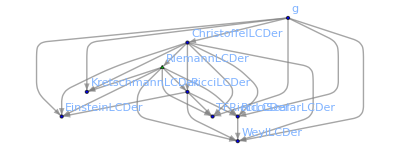

```mathematica
VariationalRelationsOf[RiemannLCDer]
```

```mathematica
DefTensor[{v[a],w[a],u[a],A[-a],B[]},M]
AddVariationalRelation[v->w->u]
AddVariationalRelation[A->B->w]
```

** DefTensor: Defining tensor v[a].

** DefTensor: Defining tensor dlv[a].

** DefTensor: Defining tensor VariationalVectorv[-a].

** DefTensor: Defining tensor w[a].

** DefTensor: Defining tensor dlw[a].

** DefTensor: Defining tensor VariationalVectorw[-a].

** DefTensor: Defining tensor u[a].

** DefTensor: Defining tensor dlu[a].

** DefTensor: Defining tensor VariationalVectoru[-a].

** DefTensor: Defining tensor A[-a].

** DefTensor: Defining tensor dlA[-a].

** DefTensor: Defining tensor VariationalVectorA[a].

** DefTensor: Defining tensor B[].

** DefTensor: Defining tensor dlB[].

** DefTensor: Defining tensor VariationalVectorB[].

** AddVariationalRelation: Variational relation created v→w.

** AddVariationalRelation: Variational relation created w→u.

** AddVariationalRelation: Variational relation created A→B.

** AddVariationalRelation: Variational relation created B→w.

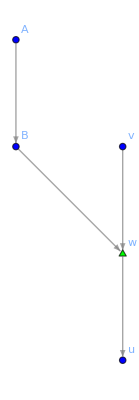

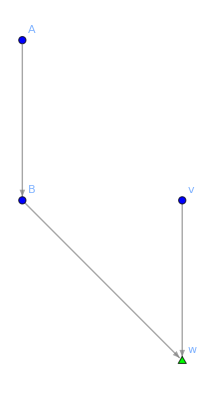

```mathematica
VariationalRelationsOf[w]
VariationalRelationsOf[w,Directed->In]
```

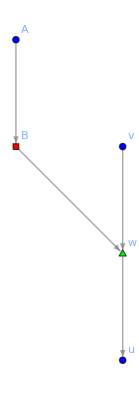

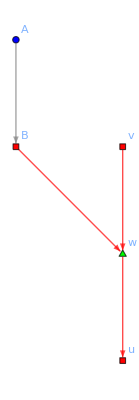

```mathematica
VariationalRelationsOf[w,ConstantTensors->{B}]
VariationalRelationsOf[w,ConstantTensors->{B,v}]
```

### 4.5 Variational relations

```mathematica
DefTensor[beta[-a,-b],M,VertDeg->2,PrintAs->"β"]
GenerateExpandVertDiffRule[{dlbeta[-a,-b],dlalpha[-a]⩕ alpha[-b] }]
dlbeta[-a,-b]==(dlbeta[-a,-b]//ExpandVertDiff[])
```

** DefTensor: Defining tensor beta[-a,-b].

** DefTensor: Defining tensor dlbeta[-a,-b].

** DefTensor: Defining tensor VariationalVectorbeta[a,b].

** GenerateExpandVertDiffRule: Expansion formula generated for dlbeta.

** GenerateExpandVertDiffRule: No variational relation added because dlbeta has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

(ⅆβ) |   |  
a | b==(ⅆα) |  
a⩕α |  
b

```mathematica
GenerateExpandVertDiffRule[{dlalpha[-a],alpha[b]⩕ dlg[-a,-b]}]
dlbeta[-a,-b]==(dlbeta[-a,-b]//ExpandVertDiff[])
```

** GenerateExpandVertDiffRule: Expansion formula generated for dlalpha.

** GenerateExpandVertDiffRule: No variational relation added because dlalpha has VertDeg≠1. If necessary, they can be added manually using AddVariationalRelation.

(ⅆβ) |   |  
a | b==g | c | d
  |   (α |  
d⩕(ⅆg) |   |  
a | c⩕α |  
b)

```mathematica
VertDiff[LCDer[-a][alpha[-b]]]==(VertDiff[LCDer[-a][alpha[-b]]]//ExpandVertDiff[])//ContractMetric//Simplification
```

ⅆ[D_a α |  
b]==1/2 (3 (α | c
 ⩕D_a(ⅆg) |   |  
b | c)+α | c
 ⩕D_b(ⅆg) |   |  
a | c-α | c
 ⩕D_c(ⅆg) |   |  
a | b+2 (D_a α | c
 ⩕(ⅆg) |   |  
b | c))

```mathematica
VertDiff[ChristoffelLCDer[a,-b,-c]]==(VertDiff[ChristoffelLCDer[a,-b,-c]] //ExpandVertDiff[])
```

(ⅆΓ[D]) | a |   |  
  | b | c==1/2 g | a | d
  |   (D_b(ⅆg) |   |  
d | c+D_c(ⅆg) |   |  
b | d-D_d(ⅆg) |   |  
b | c)

```mathematica
expr=VertDiff[RiemannLCDer[-a,-b,-c,d]];
expr//ExpandVertDiff[]//ContractMetric//Simplification
expr//ExpandVertDiff[HoldExpandVertDiff->ChristoffelLCDer]//ContractMetric//Simplification
```

1/2 (-(D_a D_b(ⅆg) |   | d
c |  )-D_a D_c(ⅆg) |   | d
b |  +D_a D^d(ⅆg) |   |  
b | c+D_b D_a(ⅆg) |   | d
c |  +D_b D_c(ⅆg) |   | d
a |  -D_b D^d(ⅆg) |   |  
a | c)

-(D_a(ⅆΓ[D]) | d |   |  
  | b | c)+D_b(ⅆΓ[D]) | d |   |  
  | a | c

```mathematica
expr=dlRicciScalarLCDer[];
expr//ExpandVertDiff[]//ContractMetric//Simplification
expr//ExpandVertDiff[HoldExpandVertDiff->RiemannLCDer]//ContractMetric//Simplification
expr//ExpandVertDiff[ConstantTensors->RiemannLCDer]//ContractMetric//Simplification
```

-(ⅆg) | a | b
  |   R[D] |   |  
a | b+D_b D_a(ⅆg) | a | b
  |  -D_b D^b(ⅆg) | a |  
  | a

(ⅆR[D]) | a | b |   |  
  |   | a | b-2 (ⅆg) | a | b
  |   R[D] |   |  
a | b

-2 (ⅆg) | a | b
  |   R[D] |   |  
a | b

### 4.7 Divergences and reconstruction of potentials

#### 4.7.1 DivergenceQ

```mathematica
expr1=LCDer[-a][xi[a]phi[]]
DivergenceQ[g][expr1]
```

ξ | a
  (D_a ϕ)+ϕ (D_a ξ | a
 )

True

```mathematica
expr2=LCDer[-a]@LCDer[-b][LCDer[a][xi[b]phi[]]-LCDer[b][xi[a]phi[]]]//Simplification
DivergenceQ[g][expr2]
DivergenceQ[g][expr2]//SortCovDs//Simplification
```

-ϕ (D_a D_b D^b ξ | a
 )+(D_a D_b ξ | b
 ) (D^a ϕ)-(D^a ϕ) (D_b D_a ξ | b
 )+ϕ (D_b D_a D^b ξ | a
 )+ξ | a
  (-(D_a D_b D^b ϕ)+D_b D^b D_a ϕ)

D_a D_b D^b ξ | a
 ==D_b D_a D^b ξ | a
 &&g | a | b
  |   (ϕ (D_c D_d D^d ξ | c
 )-(D_c D_d ξ | d
 ) (D^c ϕ)+(D^c ϕ) (D_d D_c ξ | d
 )-ϕ (D_d D_c D^d ξ | c
 )+ξ | c
  (D_c D_d D^d ϕ-D_d D^d D_c ϕ))==0

True

```mathematica
NonDivergence=phi[] LCDer[-a][xi[a]]
DivergenceQ[g][NonDivergence]
DivergenceQ[g,CheckZero->True][NonDivergence]
```

ϕ (D_a ξ | a
 )

D_a ϕ==0&&D_a ξ | a
 ==0&&g | a | b
  |   ξ | c
  (D_c ϕ)==0

False

#### 4.7.1 FindPotentialGradient

```mathematica
expr=LCDer[-a][LCDer[-b]@v[b]LCDer[-c]@alpha[-d]+alpha[-c]⩕ alpha[-d]]
FindPotentialGradient[LCDer][expr]
```

α |  
c⩕D_a α |  
d+D_a α |  
c⩕α |  
d+(D_a D_c α |  
d) (D_b v | b
 )+(D_a D_b v | b
 ) (D_c α |  
d)

(n_D) |  
a (α |  
c⩕α |  
d+(D_b v | b
 ) (D_c α |  
d))

```mathematica
expr=phi[]LCDer[-a][phi[]]
FindPotentialGradient[LCDer,3][expr]
```

ϕ (D_a ϕ)

1/2 (n_D) |  
a ϕ^2

```mathematica
expr=v[b]LCDer[-a][v[-b]]
FindPotentialGradient[LCDer][expr]
```

v | b
  (D_a v |  
b)

1/2 (n_D) |  
a v |  
b v | b

## 5. Variational calculus

### 5.1 First variation

```mathematica
VarD[g[-a,-b],LCDer][RicciScalarLCDer[]]
```

0

```mathematica
LScl=1/2 g[a,b]LCDer[-a]@phi[]LCDer[-b]@phi[] √(-Detg[]);
FirstVariation[phi][LScl]
FirstVariation[][LScl]
```

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_D) | a
  (D_a ϕ)]-√(-g^OverTilde[~]) (ⅆϕ) (D_b D^b ϕ)

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_D) | a
  (D_a ϕ)]-√(-g^OverTilde[~]) (ⅆϕ) (D_b D^b ϕ)+(ⅆg) |   |  
a | b (-1/2 √(-g^OverTilde[~]) (D^a ϕ) (D^b ϕ)+1/4 √(-g^OverTilde[~]) g | a | b
  |   (D_c ϕ) (D^c ϕ))

### 5.2 EOM

```mathematica
Lhigh=LCDer[-a]@LCDer[-c]@RiemannLCDer[a,b,c,d]LCDer[-b]@LCDer[-d]@phi[] √(-Detg[])
Timing[EOM[phi][Lhigh]]
```

√(-g^OverTilde[~]) (D_a D_c R[D] | a | b | c | d
  |   |   |  ) (D_d D_b ϕ)

{0.109375,√(-g^OverTilde[~]) g | a | e
  |   g | b | f
  |   g | c | h
  |   g | d | i
  |   (D_b D_d D_a D_c R[D] |   |   |   |  
e | f | h | i)}

```mathematica
<<xAct`xPert`;
{DefMetricPerturbation[g,pertg,ϵ];$CovDFormat="Prefix";};
DefTensorPerturbation[pertphi[LI[1]],phi[],M]
Timing[VarD[pertphi[LI[1]],LCDer][(Perturbation[Lhigh,1]//ExpandPerturbation)]]
```

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2026, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $CovDFormat changed from Prefix to Postfix

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

** DefParameter: Defining parameter ϵ.

** DefTensor: Defining tensor pertg[LI[order],-a,-b].

** DefTensor: Defining tensor dlpertg[LI[order],-a,-b].

** DefTensor: Defining tensor VariationalVectorpertg[-LI[order],a,b].

** DefTensor: Defining tensor pertphi[LI[order]].

** DefTensor: Defining tensor dlpertphi[LI[order]].

** DefTensor: Defining tensor VariationalVectorpertphi[-LI[order]].

{0.171875,δ |   | 1
1 |   √(-g^OverTilde[~]) (D_d D_b D_c D_a R[D] | a | b | c | d
  |   |   |  )}

### 5.3 EnergyMomentum

```mathematica
EnergyMomentum[LScl]//ContractMetric//Simplification
-2/(√(-Detg[]))EOM[g][LScl]//ContractMetric//Simplification
```

(D^a ϕ) (D^b ϕ)-1/2 g | a | b
  |   (D_c ϕ) (D^c ϕ)

(D^a ϕ) (D^b ϕ)-1/2 g | a | b
  |   (D_c ϕ) (D^c ϕ)

### 5.4 Symplectic potential and SymplecticCurrent

```mathematica
SymplecticPotential[phi][LScl]//ContractMetric//Simplification
SymplecticCurrent[phi][LScl]//Simplification
SymplecticCurrent[][LScl]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (ⅆϕ) (n_D) | a
  (D_a ϕ)

-√(-g^OverTilde[~]) (n_D) | a
  ((ⅆϕ)⩕D_a(ⅆϕ))

-1/2 √(-g^OverTilde[~]) (n_D) | a
  (2 ((ⅆϕ)⩕D_a(ⅆϕ))+((ⅆϕ)⩕(ⅆg) | b |  
  | b) (D_a ϕ)-2 ((ⅆϕ)⩕(ⅆg) |   |  
a | b) (D^b ϕ))

### 5.4 Noether symmetries, potentials, and currents

#### 5.4.1 NoetherSymmetryQ

```mathematica
vvf1=VVFFromLieD[xi][phi]
NoetherSymmetryQ[vvf1][g][LScl]
NoetherSymmetryQ[vvf1][g,CheckZero->True][LScl]
```

(δ/δϕ) (ℒ_ξ ϕ)

(D_a ϕ) (D_b D^b ϕ)==0&&(D^c ϕ) ((D^a ξ |  
c) (D^b ϕ)+(D^a ϕ) (D^b ξ |  
c)-g | a | b
  |   (D_d ξ |  
c) (D^d ϕ))+ξ | c
  ((D^b ϕ) (D_c D^a ϕ)+(D^a ϕ) (D_c D^b ϕ)-g | a | b
  |   (D_d D_c ϕ) (D^d ϕ))==0&&ξ | a
  (D_a D_b D^b ϕ)+(D_a ξ | a
 ) (D_b D^b ϕ)==(D^a ϕ) (D_b D^b ξ |  
a)+ξ | a
  (D_b D^b D_a ϕ)+2 (D_b D_a ϕ) (D^b ξ | a
 )

False

```mathematica
vvf2=VVFFromLieD[xi][phi,g]
NoetherSymmetryQ[vvf2][g][LScl]
NoetherSymmetryQ[vvf2][g][LScl]//SortCovDs//Simplification
```

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)+(δ/δϕ) (ℒ_ξ ϕ)

(D_a D_b ξ | b
 ) (D^a ϕ)+ξ | a
  (D_b D^b D_a ϕ)==ξ | a
  (D_a D_b D^b ϕ)+(D^a ϕ) (D_b D_a ξ | b
 )

True

#### 5.4.2 SymmetryPotential

```mathematica
SymmetryPotential[vvf1][g][LScl]
```

ToCanonical::cmods: Detected metric-incompatible derivatives {LieD[ξ | a
 ]}.

FindPotentialGradient::loopzero: Loop detected at iteration 2. Search aborted. Provide the optional 'iteration' argument to obtain partial results or try applying intermediate simplification functions.

0

```mathematica
SymmetryPotential[vvf1][g,1][LScl]//Quiet
SymmetryPotential[vvf1][g,2][LScl]//Quiet
SymmetryPotential[vvf1][g,3][LScl]
```

1/2 √(-g^OverTilde[~]) (n_D) |  
a ξ | a
  (D_b ϕ) (D^b ϕ)

1/2 √(-g^OverTilde[~]) (n_D) |  
a (2 ϕ (D^a ξ |  
b)+ξ | a
  (D_b ϕ)) (D^b ϕ)

ToCanonical::cmods: Detected metric-incompatible derivatives {LieD[ξ | a
 ]}.

FindPotentialGradient::loop: Loop detected at iteration 2. Returning the accumulated potential. Try applying intermediate simplification functions.

1/2 √(-g^OverTilde[~]) (n_D) |  
a ξ | a
  (D_b ϕ) (D^b ϕ)

```mathematica
SymmetryPotential[vvf2][g][LScl]//Quiet
```

1/2 √(-g^OverTilde[~]) (n_D) |  
a ξ | a
  (D_b ϕ) (D^b ϕ)

#### 5.4.3 NoetherCurrent

```mathematica
NoetherCurrent[vvf2][g][LScl]//ContractMetric//Simplification//Quiet
```

1/2 √(-g^OverTilde[~]) (n_D) | a
  (ξ |  
a (D_b ϕ) (D^b ϕ)-2 (D_a ϕ) (ℒ_ξ ϕ))

```mathematica
-√(-Detg[])NormalOfLCDer[-a]xi[-b]EnergyMomentum[LScl,{a,b}]//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (n_D) | a
  (D_b ϕ) (-2 ξ | b
  (D_a ϕ)+ξ |  
a (D^b ϕ))

#### 5.4.3 Non-NoetherCurrent

```mathematica
CurrentFromVector[xi][phi,LCDer][LScl]//ContractMetric//Simplification//Quiet
```

1/2 √(-g^OverTilde[~]) (n_D) | a
  (ξ |  
a (D_b ϕ) (D^b ϕ)-2 (D_a ϕ) (ℒ_ξ ϕ))

## 6. Some complicated examples

### 6.1 Scalar field and General Relativity

```mathematica
Quit[]
ClearAll[`*`]
```

```mathematica
<<xAct`xCPS`
{$PrePrint=ScreenDollarIndices;SetOptions[ContractMetric,AllowUpperDerivatives -> True];};
DefManifold[M,4,{a,b,c,d,e,f,h,i,j,k,l}] 
DefMetric[-1,g[-a,-b],LCDer,{";","D"}] 
DefTensor[phi[],M,PrintAs->"ϕ"]
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCPS` version 1.1.0, {2026,5,23}

CopyRight (C) 2025, Juan Margalef-Bentabol and Laura Sánchez Cotta, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining tensor NormalOfPDOfM[-a].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfM[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfM[a].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfM.

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining tensor dlg[-a,-b].

** DefTensor: Defining tensor VariationalVectorg[a,b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor dlepsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorepsilong[a,b,c,d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorTetrag[a,b,c,d].

** DefTensor: Defining tensor VariationalVectorTetrag†[a,b,c,d].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefCovD: Defining covariant derivative LCDer[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCDer[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDer[-a,b,c].

** DefTensor: Defining Riemann tensor RiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlRiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorRiemannLCDer[a,b,c,d].

** DefTensor: Defining symmetric Ricci tensor RicciLCDer[-a,-b].

** DefTensor: Defining tensor dlRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorRicciLCDer[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDer[].

** DefTensor: Defining tensor dlRicciScalarLCDer[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDer[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDer[-a,-b].

** DefTensor: Defining tensor dlEinsteinLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDer[a,b].

** DefTensor: Defining Weyl tensor WeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlWeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorWeylLCDer[a,b,c,d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDer[-a,-b].

** DefTensor: Defining tensor dlTFRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDer[a,b].

** DefTensor: Defining Kretschmann scalar KretschmannLCDer[].

** DefTensor: Defining tensor dlKretschmannLCDer[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDer[].

** DefCovD: Computing RiemannToWeylRules for dim 4

** DefCovD: Computing RicciToTFRicci for dim 4

** DefCovD: Computing RicciToEinsteinRules for dim 4

** DefInertHead: Defining inert head TotalDerivativeOfLCDer.

** DefTensor: Defining tensor NormalOfLCDer[-a].

** DefTensor: Defining tensor dlNormalOfLCDer[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDer[a].

** AddVariationalRelation: Variational relations created for LCDer.

** DefTensor: Defining weight +2 density Detg[].      Determinant.

** DefTensor: Defining tensor dlDetg[].

** DefTensor: Defining tensor VariationalVectorDetg[].

** DefTensor: Defining tensor dlInvg[a,b].

** DefTensor: Defining tensor VariationalVectorInvg[-a,-b].

** AddVariationalRelation: Variational relations created for g.

** DefTensor: Defining tensor phi[].

** DefTensor: Defining tensor dlphi[].

** DefTensor: Defining tensor VariationalVectorphi[].

#### First variation

```mathematica
LScl=1/2 √(-Detg[]) LCDer[-a]@phi[] LCDer[a]@phi[] 
LGR=√(-Detg[])RicciScalarLCDer[]
FirstVariation[phi][LScl]
FirstVariation[][LGR]//Simplification
```

1/2 √(-g^OverTilde[~]) (D_a ϕ) (D^a ϕ)

√(-g^OverTilde[~]) R[D]

TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (ⅆϕ) (n_D) | a
  (D_a ϕ)]-√(-g^OverTilde[~]) (ⅆϕ) (D_a D^a ϕ)

1/2 √(-g^OverTilde[~]) (ⅆg) | a | b
  |   (-2 R[D] |   |  
a | b+g |   |  
a | b R[D])+TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (n_D) | a
  (-(D_a(ⅆg) | b |  
  | b)+D_b(ⅆg) |   | b
a |  )]

```mathematica
VertDiff[g][-a,-b]
$UseInverseMetric=True;
VertDiff[g][-a,-b]
FirstVariation[][LGR] //Simplification
$UseInverseMetric=False;
```

(ⅆg) |   |  
a | b

-ⅆ(g^-1) |   |  
a | b

1/2 √(-g^OverTilde[~]) ⅆ(g^-1) | a | b
  |   (2 R[D] |   |  
a | b-g |   |  
a | b R[D])+TotalDerivativeOfLCDer[√(-g^OverTilde[~]) (n_D) | a
  (D_a ⅆ(g^-1) | b |  
  | b-D_b ⅆ(g^-1) |   | b
a |  )]

#### Equations of motion

```mathematica
WaveEq=EOM[phi][LScl]//ContractMetric
EinsteinEq=EOM[g][LGR]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) (D_a D^a ϕ)

1/2 √(-g^OverTilde[~]) (-2 R[D] | a | b
  |  +g | a | b
  |   R[D])

#### Energy-momentum tensor of the scalar field

```mathematica
EnMomScl=EnergyMomentum[LScl]//ContractMetric//Simplification
```

(D^a ϕ) (D^b ϕ)-1/2 g | a | b
  |   (D_c ϕ) (D^c ϕ)

#### Wald entropy of General Relativity

```mathematica
EntropyGR=EOM[RiemannLCDer][LGR]//Simplification
```

1/2 √(-g^OverTilde[~]) (-g | a | d
  |   g | b | c
  |  +g | a | c
  |   g | b | d
  |  )

#### Symplectic currents

```mathematica
ΩScl=SymplecticCurrent[phi][LScl]//ContractMetric//Simplification
ΩGR=SymplecticCurrent[][LGR]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) (n_D) | a
  ((ⅆϕ)⩕D_a(ⅆϕ))

1/2 √(-g^OverTilde[~]) (n_D) | a
  ((ⅆg) |   | b
a |  ⩕D_b(ⅆg) | c |  
  | c-(ⅆg) | b |  
  | b⩕D_a(ⅆg) | c |  
  | c+(ⅆg) | b |  
  | b⩕D_c(ⅆg) |   | c
a |  +(ⅆg) | b | c
  |  ⩕D_a(ⅆg) |   |  
b | c-2 ((ⅆg) | b | c
  |  ⩕D_c(ⅆg) |   |  
a | b))

#### Noether symmetries

```mathematica
DefTensor[xi[a],M,PrintAs->"ξ"]
vvf1=VVFFromLieD[xi][phi]
vvf2=VVFFromLieD[xi][phi,g]
NoetherSymmetryQ[vvf1][g,CheckZero->True][LScl]//SortCovDs//Simplification
NoetherSymmetryQ[vvf2][g][LScl]//SortCovDs//Simplification
```

** DefTensor: Defining tensor xi[a].

** DefTensor: Defining tensor dlxi[a].

** DefTensor: Defining tensor VariationalVectorxi[-a].

(δ/δϕ) (ℒ_ξ ϕ)

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)+(δ/δϕ) (ℒ_ξ ϕ)

False

True

```mathematica
{BianchiContracted1=MakeRule[{LCDer[-e]@RiemannLCDer[-a,-c,-d,e],$RicciSign(LCDer[-c]@RicciLCDer[-a,-d]-LCDer[-a]@RicciLCDer[-c,-d])},MetricOn->All];
BianchiContracted2=MakeRule[{LCDer[-b]@RicciScalarLCDer[],2LCDer[-a][RicciLCDer[a,-b]]},MetricOn->All];
BianchiRiemann=MakeRule[{RiemannLCDer[a,b,c,d],RiemannLCDer[a,c,b,d]-RiemannLCDer[a,d,b,c],OrderedQ[{a,b,c,d}]},MetricOn->All];
ApplyBianchi[expr_]:=expr//.BianchiContracted1//.BianchiContracted2//.BianchiRiemann};

vvf3=VVFFromLieD[xi][g]
NoetherSymmetryQ[vvf3][g][LGR]//SortCovDs//Simplification//ApplyBianchi//ContractMetric//Simplification
```

(δ/δg) | a | b
  |   (ℒ_ξ g |   |  
a | b)

True

#### Noether currents of the scalar field

```mathematica
NoetherCurrent[vvf1][g][LScl]//ContractMetric//Simplification
NoetherCurrent[vvf2][g][LScl]//ContractMetric//Simplification//Quiet
```

ToCanonical::cmods: Detected metric-incompatible derivatives {LieD[ξ | a
 ]}.

FindPotentialGradient::loopzero: Loop detected at iteration 2. Search aborted. Provide the optional 'iteration' argument to obtain partial results or try applying intermediate simplification functions.

ToCanonical::cmods: Detected metric-incompatible derivatives {LieD[ξ | a
 ]}.

-√(-g^OverTilde[~]) (n_D) | a
  (D_a ϕ) (ℒ_ξ ϕ)

1/2 √(-g^OverTilde[~]) (n_D) | a
  (ξ |  
a (D_b ϕ) (D^b ϕ)-2 (D_a ϕ) (ℒ_ξ ϕ))

#### Non-Noether currents of the scalar field

```mathematica
CurrentFromVector[xi][LCDer][LScl]//LieDToCovD[#,LCDer]&//ContractMetric//Simplification
```

1/2 √(-g^OverTilde[~]) (n_D) | a
  (D_b ϕ) (-2 ξ | b
  (D_a ϕ)+ξ |  
a (D^b ϕ))

#### Noether currents of GR

```mathematica
NoetherCurrent[vvf3][g][LGR]//ContractMetric//Simplification
```

FindPotentialGradient::loopzero: Loop detected at iteration 4. Search aborted. Provide the optional 'iteration' argument to obtain partial results or try applying intermediate simplification functions.

√(-g^OverTilde[~]) g | b | c
  |   (n_D) | a
  (D_a ℒ_ξ g |   |  
b | c-D_c ℒ_ξ g |   |  
a | b)

```mathematica
SymmetryPotential[vvf3][g][LGR,SortCovDs,ApplyBianchi]
NoetherCurrent[vvf3][g][LGR,ApplyBianchi]//LieDToCovD[#,LCDer]&//SortCovDs//ContractMetric//
Simplification
```

√(-g^OverTilde[~]) (n_D) |  
a R[D] ξ | a

√(-g^OverTilde[~]) (n_D) | a
  (R[D] ξ |  
a-2 R[D] |   |  
a | b ξ | b
 )

```mathematica
NoetherCurrent[vvf3][g][LGR,ApplyBianchi,SortCovDs]//LieDToCovD[#,LCDer]&//SortCovDs//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_D) | a
  (R[D] ξ |  
a-2 R[D] |   |  
a | b ξ | b
 +D_b D_a ξ | b
 -D_b D^b ξ |  
a)

### 6.2 EM

```mathematica
Quit[]
ClearAll[`*`]
```

```mathematica
<<xAct`xCPS`
{$PrePrint=ScreenDollarIndices;SetOptions[ContractMetric,AllowUpperDerivatives -> True];};
DefManifold[M,4,{a,b,c,d,e,f,h,i,j,k,l}] 
DefMetric[-1,g[-a,-b],LCDer,{";","D"}] 
DefTensor[A[-a],M]
DefTensor[F[-a,-b],M,Antisymmetric[{-a,-b}]]
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCPS` version 1.1.0, {2026,5,23}

CopyRight (C) 2025, Juan Margalef-Bentabol and Laura Sánchez Cotta, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining tensor NormalOfPDOfM[-a].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfM[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfM[a].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfM.

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining tensor dlg[-a,-b].

** DefTensor: Defining tensor VariationalVectorg[a,b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor dlepsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorepsilong[a,b,c,d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorTetrag[a,b,c,d].

** DefTensor: Defining tensor VariationalVectorTetrag†[a,b,c,d].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefCovD: Defining covariant derivative LCDer[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCDer[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDer[-a,b,c].

** DefTensor: Defining Riemann tensor RiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlRiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorRiemannLCDer[a,b,c,d].

** DefTensor: Defining symmetric Ricci tensor RicciLCDer[-a,-b].

** DefTensor: Defining tensor dlRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorRicciLCDer[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDer[].

** DefTensor: Defining tensor dlRicciScalarLCDer[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDer[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDer[-a,-b].

** DefTensor: Defining tensor dlEinsteinLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDer[a,b].

** DefTensor: Defining Weyl tensor WeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlWeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorWeylLCDer[a,b,c,d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDer[-a,-b].

** DefTensor: Defining tensor dlTFRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDer[a,b].

** DefTensor: Defining Kretschmann scalar KretschmannLCDer[].

** DefTensor: Defining tensor dlKretschmannLCDer[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDer[].

** DefCovD: Computing RiemannToWeylRules for dim 4

** DefCovD: Computing RicciToTFRicci for dim 4

** DefCovD: Computing RicciToEinsteinRules for dim 4

** DefInertHead: Defining inert head TotalDerivativeOfLCDer.

** DefTensor: Defining tensor NormalOfLCDer[-a].

** DefTensor: Defining tensor dlNormalOfLCDer[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDer[a].

** AddVariationalRelation: Variational relations created for LCDer.

** DefTensor: Defining weight +2 density Detg[].      Determinant.

** DefTensor: Defining tensor dlDetg[].

** DefTensor: Defining tensor VariationalVectorDetg[].

** DefTensor: Defining tensor dlInvg[a,b].

** DefTensor: Defining tensor VariationalVectorInvg[-a,-b].

** AddVariationalRelation: Variational relations created for g.

** DefTensor: Defining tensor A[-a].

** DefTensor: Defining tensor dlA[-a].

** DefTensor: Defining tensor VariationalVectorA[a].

** DefTensor: Defining tensor F[-a,-b].

** DefTensor: Defining tensor dlF[-a,-b].

** DefTensor: Defining tensor VariationalVectorF[a,b].

#### First variation

```mathematica
LEM=1/4 √(-Detg[])F[-a,-b]F[a,b]
GenerateExpandVertDiffRule[{dlF[-a,-b],LCDer[-a]@dlA[-b]-LCDer[-b]@dlA[-a]}]
VertDiff[F[-a,-b]]//ExpandVertDiff[]
```

1/4 √(-g^OverTilde[~]) F |   |  
a | b F | a | b
  |

** GenerateExpandVertDiffRule: Expansion formula generated for dlF.

** AddVariationalRelation: Variational relation created A→F.

D_a(ⅆA) |  
b-D_b(ⅆA) |  
a

```mathematica
FirstVariation[A,LCDer][LEM]
```

TotalDerivativeOfLCDer[-√(-g^OverTilde[~]) (ⅆA) | a
  F |   |  
a | b (n_D) | b
 ]+√(-g^OverTilde[~]) (ⅆA) |  
a (D_b F | a | b
  |  )

#### Energy-momentum tensor

```mathematica
EnMomEM=EnergyMomentum[LEM]//ContractMetric//Simplification
```

F | a | c
  |   F | b |  
  | c-1/4 F |   |  
c | d F | c | d
  |   g | a | b
  |

#### Symplectic currents

```mathematica
SymplecticCurrent[A,LCDer][LEM]//ContractMetric//Simplification
SymplecticCurrent[A,LCDer,HoldExpandVertDiff->F][LEM]//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_D) | a
  (-((ⅆA) | b
 ⩕D_a(ⅆA) |  
b)+(ⅆA) | b
 ⩕D_b(ⅆA) |  
a)

-√(-g^OverTilde[~]) (n_D) | a
  ((ⅆA) | b
 ⩕(ⅆF) |   |  
a | b)

#### Noether symmetries

```mathematica
DefTensor[lambda[],M,PrintAs->"λ"]
DefTensor[xi[a],M,PrintAs->"ξ"]
vvfEM1=LCDer[-a]@lambda[]VariationalVectorA[a]
vvfEM2=VVFFromLieD[xi][A]
NoetherSymmetryQ[vvfEM1][g][LEM]
NoetherSymmetryQ[vvfEM2][g,CheckZero->True][LEM]
```

** DefTensor: Defining tensor lambda[].

** DefTensor: Defining tensor dllambda[].

** DefTensor: Defining tensor VariationalVectorlambda[].

** DefTensor: Defining tensor xi[a].

** DefTensor: Defining tensor dlxi[a].

** DefTensor: Defining tensor VariationalVectorxi[-a].

(δ/δA) | a
  (D_a λ)

(δ/δA) | a
  (ℒ_ξ A |  
a)

True

False

#### Noether current

```mathematica
NoetherCurrent[vvfEM1][LCDer][LEM]//ContractMetric//Simplification
```

-√(-g^OverTilde[~]) F |   |  
a | b (n_D) | a
  (D^b λ)

#### Non-Noether current

```mathematica
CurrentFromVector[xi][A,LCDer][LEM]//LieDToCovD[#,LCDer]&//ContractMetric//Simplification
```

1/4 √(-g^OverTilde[~]) (-4 F |   |  
a | c (n_D) | a
  ξ | b
  (D_b A | c
 )+F |   |  
b | c (F | b | c
  |   (n_D) | a
  ξ |  
a-4 A | a
  (n_D) | b
  (D^c ξ |  
a)))

### 6.3 f(Riemann)

```mathematica
Quit[]
ClearAll[`*`]
```

```mathematica
<<xAct`xCPS`
{$PrePrint=ScreenDollarIndices;SetOptions[ContractMetric,AllowUpperDerivatives -> True];};
DefManifold[M,4,{a,b,c,d,e,f,h,i,j,k,l}] 
DefMetric[-1,g[-a,-b],LCDer,{";","D"}] 
PrintAs[RiemannLCDer]^="Riem";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.4, {2025,12,29}

CopyRight (C) 2003-2026, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor` version 1.3.0, {2025,12,29}

CopyRight (C) 2002-2026, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCPS` version 1.1.0, {2026,5,3}

CopyRight (C) 2025, Juan Margalef-Bentabol and Laura Sánchez Cotta, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefTensor: Defining tensor NormalOfPDOfM[-a].

** DefTensor: Defining vanishing tensor dlNormalOfPDOfM[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfPDOfM[a].

** DefInertHead: Defining inert head TotalDerivativeOfPDOfM.

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining tensor dlg[-a,-b].

** DefTensor: Defining tensor VariationalVectorg[a,b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor dlepsilong[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorepsilong[a,b,c,d].

** DefTensor: Defining tetrametric Tetrag[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag[-a,-b,-c,-d].

** DefTensor: Defining tensor dlTetrag†[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorTetrag[a,b,c,d].

** DefTensor: Defining tensor VariationalVectorTetrag†[a,b,c,d].

** AddVariationalRelation: Variational relations created for conjugated tensors

** DefCovD: Defining covariant derivative LCDer[-a].

** DefTensor: Defining vanishing torsion tensor TorsionLCDer[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor dlChristoffelLCDer[a,-b,-c].

** DefTensor: Defining tensor VariationalVectorChristoffelLCDer[-a,b,c].

** DefTensor: Defining Riemann tensor RiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlRiemannLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorRiemannLCDer[a,b,c,d].

** DefTensor: Defining symmetric Ricci tensor RicciLCDer[-a,-b].

** DefTensor: Defining tensor dlRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorRicciLCDer[a,b].

** DefCovD: Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarLCDer[].

** DefTensor: Defining tensor dlRicciScalarLCDer[].

** DefTensor: Defining tensor VariationalVectorRicciScalarLCDer[].

** DefCovD: Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinLCDer[-a,-b].

** DefTensor: Defining tensor dlEinsteinLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorEinsteinLCDer[a,b].

** DefTensor: Defining Weyl tensor WeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor dlWeylLCDer[-a,-b,-c,-d].

** DefTensor: Defining tensor VariationalVectorWeylLCDer[a,b,c,d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciLCDer[-a,-b].

** DefTensor: Defining tensor dlTFRicciLCDer[-a,-b].

** DefTensor: Defining tensor VariationalVectorTFRicciLCDer[a,b].

** DefTensor: Defining Kretschmann scalar KretschmannLCDer[].

** DefTensor: Defining tensor dlKretschmannLCDer[].

** DefTensor: Defining tensor VariationalVectorKretschmannLCDer[].

** DefCovD: Computing RiemannToWeylRules for dim 4

** DefCovD: Computing RicciToTFRicci for dim 4

** DefCovD: Computing RicciToEinsteinRules for dim 4

** DefInertHead: Defining inert head TotalDerivativeOfLCDer.

** DefTensor: Defining tensor NormalOfLCDer[-a].

** DefTensor: Defining tensor dlNormalOfLCDer[-a].

** DefTensor: Defining tensor VariationalVectorNormalOfLCDer[a].

** AddVariationalRelation: Variational relations created for LCDer.

** DefTensor: Defining weight +2 density Detg[].      Determinant.

** DefTensor: Defining tensor dlDetg[].

** DefTensor: Defining tensor VariationalVectorDetg[].

** DefTensor: Defining tensor dlInvg[a,b].

** DefTensor: Defining tensor VariationalVectorInvg[-a,-b].

** AddVariationalRelation: Variational relations created for g.

```mathematica
DefScalarFunction[L,{RiemannLCDer}]
Ldensity=√(-Detg[])L[RiemannLCDer]
```

** DefScalarFunction: Defining scalar function L. It depends on RiemannLCDer

√(-g^OverTilde[~]) L[RiemannLCDer]

#### Equations of motion

```mathematica
EOM[g][Ldensity]//ContractMetric//Simplification
```

** DefTensor: Defining tensor PartialLPartialRiemannLCDer[a,b,c,d].

1/2 √(-g^OverTilde[~]) (g | a | b
  |   L[(RiemannLCDer)]+((∂L)/(∂Riem)) | b | c | d | e
  |   |   |   Riem | a |   |   |  
  | c | d | e+((∂L)/(∂Riem)) | a | c | d | e
  |   |   |   Riem | b |   |   |  
  | c | d | e-2 (D_c D_d((∂L)/(∂Riem)) | a | c | b | d
  |   |   |  )-2 (D_d D_c((∂L)/(∂Riem)) | a | c | b | d
  |   |   |  ))

#### Wald entropy

```mathematica
EOM[RiemannLCDer][Ldensity]//Simplification
```

√(-g^OverTilde[~]) ((∂L)/(∂Riem)) | a | b | c | d
  |   |   |

#### Symplectic currents

```mathematica
SymplecticCurrent[][Ldensity]//ContractMetric//Simplification
```

** DefTensor: Defining tensor Partial2LPartial2RiemannLCDer[a,b,c,d,e,f,h,i].

√(-g^OverTilde[~]) (n_D) | a
  (((∂L)/(∂Riem)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | d⩕D_a(ⅆg) |   |  
c | e)-2 ((∂L)/(∂Riem)) | b | c | d | e
  |   |   |   ((ⅆg) |   |  
b | d⩕D_e(ⅆg) |   |  
a | c)+2 ((∂^2 L)/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |   Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
e | j⩕D_i(ⅆg) |   |  
f | h)+((∂L)/(∂Riem)) |   | b | c | d
a |   |   |   ((ⅆg) |   |  
b | c⩕D_d(ⅆg) | e |  
  | e+2 ((ⅆg) |   | e
c |  ⩕D_b(ⅆg) |   |  
d | e)+2 ((ⅆg) |   | e
c |  ⩕D_d(ⅆg) |   |  
b | e)-2 ((ⅆg) |   | e
c |  ⩕D_e(ⅆg) |   |  
b | d)+(ⅆg) | e |  
  | e⩕D_d(ⅆg) |   |  
b | c)+2 ((∂^2 L)/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |   Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
f | h⩕D_i(ⅆg) |   |  
e | j)-4 ((∂^2 L)/(∂^2 Riem)) |   | b | c | d | e | f | h | i
a |   |   |   |   |   |   |   ((ⅆg) |   |  
b | c⩕D_d D_i D_f(ⅆg) |   |  
e | h-D_d(ⅆg) |   |  
b | c⩕D_i D_f(ⅆg) |   |  
e | h)+4 ((ⅆg) |   |  
b | d⩕D_i D_f(ⅆg) |   |  
e | h) (D_c((∂^2 L)/(∂^2 Riem)) |   | b | c | d | e | f | h | i
a |   |   |   |   |   |   |  )-((ⅆg) |   |  
b | d⩕(ⅆg) | e |  
  | e) (D_c((∂L)/(∂Riem)) |   | b | c | d
a |   |   |  )+2 ((∂^2 L)/(∂^2 Riem)) |   | h |   | i |   |   |   | j
a |   | f |   | b | c | d |   ((ⅆg) |   |  
e | j⩕(ⅆg) |   |  
h | i) (D^f Riem | b | c | d | e
  |   |   |  )+2 Riem | b | c | d | e
  |   |   |   ((ⅆg) |   |  
e | j⩕(ⅆg) |   |  
f | i) (D_h((∂^2 L)/(∂^2 Riem)) |   | f | h | i |   |   |   | j
a |   |   |   | b | c | d |  ))

```mathematica
expr=Partial2LPartial2RiemannLCDer[a,b,c,d,e,f,h,i]-Partial2LPartial2RiemannLCDer[e,f,h,i,a,b,c,d]
expr//ToCanonical
```

((∂^2 L)/(∂^2 Riem)) | a | b | c | d | e | f | h | i
  |   |   |   |   |   |   |  -((∂^2 L)/(∂^2 Riem)) | e | f | h | i | a | b | c | d
  |   |   |   |   |   |   |

0

#### Noether symmetries

```mathematica
DefTensor[xi[a],M,PrintAs->"ξ"]
vvf1=VVFFromLieD[xi][g];
NoetherSymmetryQ[vvf1][g][Ldensity][[1]]//Simplification
```

** DefTensor: Defining tensor xi[a].

** DefTensor: Defining tensor dlxi[a].

** DefTensor: Defining tensor VariationalVectorxi[-a].

Riem | b | c | d | e
  |   |   |   (D_c((∂L)/(∂Riem)) |   |   |   |  
a | b | d | e)+((∂L)/(∂Riem)) | b | c | d | e
  |   |   |   (D_c Riem |   |   |   |  
a | b | d | e)+Riem |   | b | c | d
a |   |   |   (D_e((∂L)/(∂Riem)) |   | e |   |  
b |   | c | d)+((∂L)/(∂Riem)) |   | b | c | d
a |   |   |   (D_e Riem |   | e |   |  
b |   | c | d)==D_a L[(RiemannLCDer)]+2 (D_d D_b D_c((∂L)/(∂Riem)) |   | b | c | d
a |   |   |  +D_d D_c D_b((∂L)/(∂Riem)) |   | b | c | d
a |   |   |  )

#### Non-Noether current

```mathematica
CurrentFromVector[xi][LCDer][Ldensity]//LieDToCovD[#,LCDer]&//ContractMetric//Simplification
```

√(-g^OverTilde[~]) (n_D) | a
  (L[(RiemannLCDer)] ξ |  
a+2 (D^c ξ | b
 ) (D_d((∂L)/(∂Riem)) |   |   |   | d
a | b | c |  +D_d((∂L)/(∂Riem)) |   |   |   | d
a | c | b |  )-2 (((∂L)/(∂Riem)) |   |   |   |  
a | b | c | d+((∂L)/(∂Riem)) |   |   |   |  
a | c | b | d) (D^d D^c ξ | b
 ))

#### Higher order theory

```mathematica
Implode[LCDer[-a][RiemannLCDer[-b,-c,-d,-e]]]
DefScalarFunction[L2,{RiemannLCDer,LCDerRiemannLCDer}]
Ldensity2=√(-Detg[])L2[RiemannLCDer,LCDerRiemannLCDer]
EOM[RiemannLCDer][Ldensity2]//Simplification
```

DRiem |   |   |   |   |  
b | c | d | e | a

** DefScalarFunction: Defining scalar function L2. It depends on LCDerRiemannLCDer and RiemannLCDer

√(-g^OverTilde[~]) L2[RiemannLCDer,LCDerRiemannLCDer]

** DefTensor: Defining tensor PartialL2PartialRiemannLCDer[a,b,c,d].

** DefTensor: Defining tensor PartialL2PartialLCDerRiemannLCDer[a,b,c,d,e].

√(-g^OverTilde[~]) (((∂L2)/(∂Riem)) | a | b | c | d
  |   |   |  -D_e((∂L2)/(∂DRiem)) | a | b | c | d | e
  |   |   |   |  )

```mathematica
RotateGraph[g_Graph,angle_]:=Module[{coords,center,rotatedCoords,existingOpts},
coords=GraphEmbedding[g];
center=Mean[coords];
rotatedCoords=RotationTransform[angle,center]/@coords;existingOpts=FilterRules[Options[g],Except[VertexCoordinates]];
Graph[VertexList[g],EdgeList[g],VertexCoordinates->rotatedCoords,Sequence@@existingOpts]]
```

```mathematica
<<xAct`TexAct`
(* Wedge *)
TexOperator[WWedge]:=" \\wwedge ";
Tex[expr_WWedge]:=StringJoin@@Riffle[xAct`TexAct`Private`TexFactor/@List@@expr,TexOperator[WWedge]];

(* Exterior derivative *)
TexOperator[VertDiff]:=" \\dd ";(* "\\mathbb{d}" *)
Tex["ⅆ"]="\\dd "; (* "\\mathbb{d}" *)

Tex[VertInt[a_]]:=StringJoin[" \\ii_{",Tex[a],"}"];(* "\\mathbb{i}" *)
Tex["ⅈ"]="\\ii "; (* "\\mathbb{d}" *)

Tex[VertLie[a_]]:=StringJoin[" \\LL_{",Tex[a],"}"] ; (* "\\mathbb{L}"}"]*)
Tex["LL"]="\\LL "; (* "\\mathbb{d}" *)

Tex[HoldPattern[ⅆ expr_]]:=StringJoin[" \\dd ",Tex[expr]]
Tex[HoldPattern[VertDiff[expr_WWedge|expr_Plus|expr_Times,covd___]]]:=StringJoin[TexOperator[VertDiff],If[covd===PD,"",StringJoin["^{",Tex[SymbolOfCovD[covd][[2]]],"}"]],xAct`TexAct`Private`TexOpen["("],Tex[expr],xAct`TexAct`Private`TexClose[")"]];
Tex[HoldPattern[VertDiff[expr_,covd___]]]:=StringJoin[TexOperator[VertDiff],If[covd===PD,"",StringJoin["^{",Tex[SymbolOfCovD[covd][[2]]],"}"]],Tex[expr]];

Tex[head_Symbol]/;StringStartsQ[SymbolName[head],"NormalOf"]:=Block[{derSymbol=SymbolOfCovD[CovDOfNormal[head]][[2]]},"(n_{"<>Tex[derSymbol]<>"})"]

Tex[s_Symbol]/;PartialPartialQ[s]&&!TrueQ[$FixingTex]:=Block[{$FixingTex=True},Module[{raw},raw=ToString[Tex[s]];
(*Apply cleaning only to this specific symbol's output*)StringReplace[raw,{"@!"->"","\""->""}]]];

Tex[TemplateBox[{base_,script_},"Superscript"]]:=Tex[base]<>"^{"<>Tex[script]<>"}";
```

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.5, {2025,8,9}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------